```mathematica
ClearAll["Global`*"]
```

```mathematica
dir=NotebookDirectory[];
SetDirectory@dir;
```

```mathematica
NotebookEvaluate[dir<>"../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
NotebookEvaluate[dir<>"../../Tools/Mathematica/FEinterpolants.nb"]
```

## Initial Mesh

```mathematica
Ω=Rectangle[{0,0},{1,1}];
```

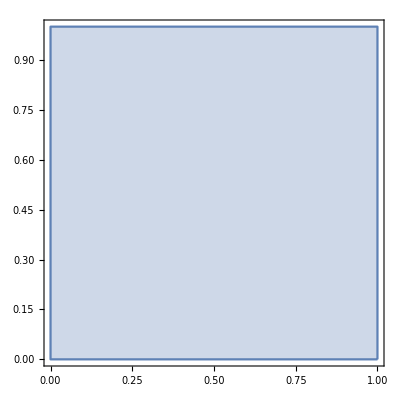

```mathematica
RegionPlot[Ω,AspectRatio->Automatic]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.1,.2];
(*𝒯=create𝒯fromRegion[Ω,.003,.05];*)
```

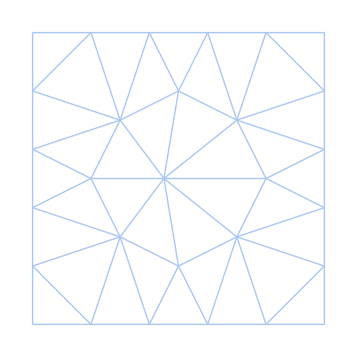

```mathematica
highlight[𝒯,{},0]
```

```mathematica
export@𝒯
```

mesh.ntn

## Fine Mesh

```mathematica
cMesh=import@"cMesh.ntnr";
fMesh=import@"fMesh.ntnr";
```

```mathematica
highlight[#,{"nodesNumn","trianglesNumn"}]&/@{cMesh,fMesh}
```

{-Graphics-,-Graphics-}

## Interpolants

```mathematica
f[x_,y_]:=2Sin[Pi x]Cos[Pi y]
```

```mathematica
Plot3D[f[x,y],{x,y}∈Ω,Mesh->None,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
FE=ΔP1CR;
```

```mathematica
fDOFs=computeDOFs[f,FE,fMesh];
Export["fDOFs.dat",fDOFs];
```

```mathematica
PfDOFs=𝒫[fDOFs,FE,fMesh];
```

```mathematica
fPlot=plot𝒫ξ[PfDOFs,fMesh,{Blue,Opacity@.7}]
```

-Graphics3D-

```mathematica
cDOFs=Import["cDOFs.dat"][[1]];
```

```mathematica
PcDOFs=𝒫[cDOFs,FE,cMesh];
```

```mathematica
Show[fPlot,plot𝒫ξ[PcDOFs,cMesh,{Green,Opacity@.7}]]
```

-Graphics3D-

## Matrices

```mathematica
lhs=Import@"lhs.rsa";
rhs=Import@"rhs.rra";
```

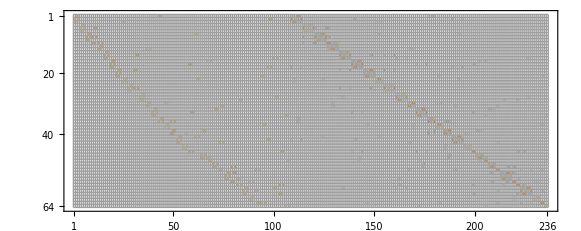

```mathematica
MatrixPlot[rhs,Mesh->All,MaxPlotPoints->Infinity]
```

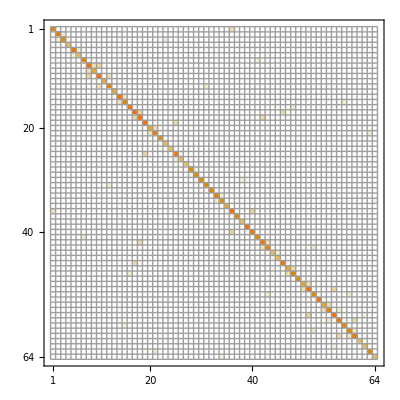

```mathematica
MatrixPlot[lhs,Mesh->All,MaxPlotPoints->Infinity]
```

```mathematica
Max@Eigenvalues@lhs/Min@Eigenvalues@lhs
```

3.5